```mathematica
3+5
6*9
```

8

54

```mathematica
myList = {1,2,3,4,5}
myList*5
```

{1,2,3,4,5}

{5,10,15,20,25}

```mathematica
NestList[#*2 &, 1, 10]*35
```

{35,70,140,280,560,1120,2240,4480,8960,17920,35840}

{1,2,4,8,16,32,64,128,256,512,1024}

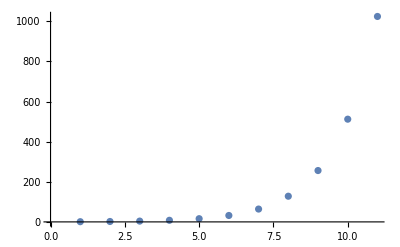

```mathematica
myList = NestList[#*2 &, 1, 10]
ListPlot[myList]
```

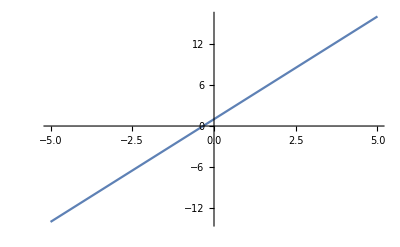

```mathematica
Plot[3 x + 1, {x, -5, 5}]
```

```mathematica
Solve[x^2 + 2 x - 7 == 0, x]
N[%]
```

{{x→-1-2 √2},{x→-1+2 √2}}

{{x→-3.82843},{x→1.82843}}

```mathematica
Integrate[x^3 = 2 x - 3, x]
```

Set::write: Tag Power in x^3 is Protected.

-3 x+x^2

```mathematica
Integrate[x^3 + 2 x - 3, x]
```

-3 x+x^2+x^4/4

```mathematica
Animate[Plot[Exp[-B x] * Sin[w x],{x,0,2 Pi}],{B,-1, 1},{w, 0, 2Pi}]
```